```mathematica
(*Define alpha function based on m and n using Piecewise*)Alpha[m_,n_]:=Piecewise[{{(-1)^m,n==1},{(-1)^(m+1)*m^2,n==2},{(-1)^(m+n-1)*2^(n-2)*m*Sum[Binomial[n+k-3,k-1]*Product[m-j,{j,k,n+k-3}],{k,1,m-n+2}],n≥3}}]
```

```mathematica
Alpha[4,2]
```

-16

```mathematica
(*Define Fourier transform of Chebyshev polynomials using Alpha function*)
FourierTn[m_,lambda_]:=Sum[Alpha[m,n]*(Exp[I*lambda]/(I*lambda)^n+(-1)^(n+m)*Exp[-I*lambda]/(I*lambda)^n),{n,1,m+1}]

(*Define the inner product with respect to J0(t)*)
InnerProduct[f_,g_]:=Integrate[f[t]*Conjugate[g[t]]*BesselJ[0,t],{t,-Infinity,Infinity}]


Integrate[FourierTn[0,t]/Pi,{t,0,Infinity}]
```

```mathematica
a[n_]:=-I*(2*(-1)^n+Sum[4*(-1)^(k+n)/(1-4*k^2),{k,1,n}])
```

```mathematica
b[n_]:=-(ⅈ (-1)^n (-2 (-1)^n+π+2 n π+2 (-1)^n (1+2 n) LerchPhi[-1,1,3/2+n]))/(1+2 n)
```

```mathematica
Simplify[Table[a[n],{n,0,20}]]
```

{-2 ⅈ,(10 ⅈ)/3,-(46 ⅈ)/15,(334 ⅈ)/105,-(982 ⅈ)/315,(10942 ⅈ)/3465,-(140986 ⅈ)/45045,(28382 ⅈ)/9009,-(2400458 ⅈ)/765765,(45788882 ⅈ)/14549535,-(45643022 ⅈ)/14549535,(1052560846 ⅈ)/334639305,-(5251164602 ⅈ)/1673196525,(15783239522 ⅈ)/5019589575,-(456970303238 ⅈ)/145568097675,(14186157758678 ⅈ)/4512611027925,-(14168513140778 ⅈ)/4512611027925,(14184141230918 ⅈ)/4512611027925,-(524297498569346 ⅈ)/166966608033225,(524760330469646 ⅈ)/166966608033225,-(21498048768944386 ⅈ)/6845630929362225}

```mathematica
Simplify[Table[b[n],{n,0,20}]]
```

{-2 ⅈ,(10 ⅈ)/3,-(46 ⅈ)/15,(334 ⅈ)/105,-(982 ⅈ)/315,(10942 ⅈ)/3465,-(140986 ⅈ)/45045,(28382 ⅈ)/9009,-(2400458 ⅈ)/765765,(45788882 ⅈ)/14549535,-(45643022 ⅈ)/14549535,(1052560846 ⅈ)/334639305,-(5251164602 ⅈ)/1673196525,(15783239522 ⅈ)/5019589575,-(456970303238 ⅈ)/145568097675,(14186157758678 ⅈ)/4512611027925,-(14168513140778 ⅈ)/4512611027925,(14184141230918 ⅈ)/4512611027925,-(524297498569346 ⅈ)/166966608033225,(524760330469646 ⅈ)/166966608033225,-(21498048768944386 ⅈ)/6845630929362225}

```mathematica
Integrate[FourierTn[1,t],{t,0,Infinity}]
```

-2 ⅈ

```mathematica
Integrate[FourierTn[2,t],{t,0,Infinity}]
```

-π

```mathematica
Integrate[FourierTn[7,t],{t,0,Infinity}]
```

(334 ⅈ)/105

```mathematica
maxN=60;(*Replace with the maximum value you're interested in*)results=Table[Integrate[FourierTn[n,t],{t,0,Infinity}],{n,1,maxN,2}]
```

{-2 ⅈ,(10 ⅈ)/3,-(46 ⅈ)/15,(334 ⅈ)/105,-(982 ⅈ)/315,(10942 ⅈ)/3465,-(140986 ⅈ)/45045,(28382 ⅈ)/9009,-(2400458 ⅈ)/765765,(45788882 ⅈ)/14549535,-(45643022 ⅈ)/14549535,(1052560846 ⅈ)/334639305,-(5251164602 ⅈ)/1673196525,(15783239522 ⅈ)/5019589575,-(456970303238 ⅈ)/145568097675,(14186157758678 ⅈ)/4512611027925,-(14168513140778 ⅈ)/4512611027925,(14184141230918 ⅈ)/4512611027925,-(524297498569346 ⅈ)/166966608033225,(524760330469646 ⅈ)/166966608033225,-(21498048768944386 ⅈ)/6845630929362225,(925083963496741498 ⅈ)/294362129962575675,-(924475462969687078 ⅈ)/294362129962575675,(43476512282238632726 ⅈ)/13835020108241056725,-(304167379044263242982 ⅈ)/96845140757687397075,(304322393275167904682 ⅈ)/96845140757687397075,-(16121491146269570524846 ⅈ)/5132792460157432044975,(16128534429233765971906 ⅈ)/5132792460157432044975,-(16121985411740742135166 ⅈ)/5132792460157432044975,(951557335254820096995494 ⅈ)/302834755149288490653525}

```mathematica
Map[Im,Out[57]]
```

{-2,10/3,-46/15,334/105,-982/315,10942/3465,-140986/45045,28382/9009,-2400458/765765,45788882/14549535,-45643022/14549535,1052560846/334639305,-5251164602/1673196525,15783239522/5019589575,-456970303238/145568097675,14186157758678/4512611027925,-14168513140778/4512611027925,14184141230918/4512611027925,-524297498569346/166966608033225,524760330469646/166966608033225,-21498048768944386/6845630929362225,925083963496741498/294362129962575675,-924475462969687078/294362129962575675,43476512282238632726/13835020108241056725,-304167379044263242982/96845140757687397075,304322393275167904682/96845140757687397075,-16121491146269570524846/5132792460157432044975,16128534429233765971906/5132792460157432044975,-16121985411740742135166/5132792460157432044975,951557335254820096995494/302834755149288490653525}

```mathematica
Table[Out[67][[n]]*(2n-1)!,{n,1,30}]
```

{-2,20,-368,16032,-1131264,126051840,-19489904640,4119704064000,-1114980094771200,382829633283686400,-160276256082690048000,81313880954560708608000,-48680424502869774827520000,34238184634794838830612480000,-27756237279807229299271925760000,25849887271574128911583071436800000,-27263528592726319675126275951820800000,32479384819167302733503010032320512000000,-43220027056069144244743952283262255104000000,64108623082766536755765673199913589014528000000,-105054458236942464101574102892002274097233920000000,189865425343503736986812892516248254489842155520000000,-375686261103412892371745934083472509853578664345600000000,812722818475339747881034736637694255627255885804339200000000,-1910467565599315165937822441929527240295857206275237478400000000,4874175075396760887675619684729769137762140173272791121920000000000,-13426900376407516623800936428616702271752827768093468545515520000000000,39895316283767248250460259890552588960772561004412832368191078400000000000,-127294140589581066346243400796282865784623360327621675940452289740800000000000,435765500769917137357675056115091550903320006572221806150643223206297600000000000}

```mathematica
FindSequenceFunction[Out[79],n]
```

((-1)^(1+n) (-1+2 n)! (-2 (-1)^n+π-2 n π-2 (-1)^n LerchPhi[-1,1,1/2+n]+4 (-1)^n n LerchPhi[-1,1,1/2+n]))/(-1+2 n)

```mathematica
FullSimplify[Out[82]]
```

((-1)^(1+n) Gamma[2 n] (-2 (-1)^n+π-2 n π+2 (-1)^n (-1+2 n) LerchPhi[-1,1,1/2+n]))/(-1+2 n)

```mathematica
a[n_]:=(((-1)^(1+n) Gamma[2 n] (-2 (-1)^n+π-2 n π+2 (-1)^n (-1+2 n) LerchPhi[-1,1,1/2+n]))/(-1+2 n))/((2n-1)!)
```

```mathematica
FullSimplify[a[3]]
```

-46/15

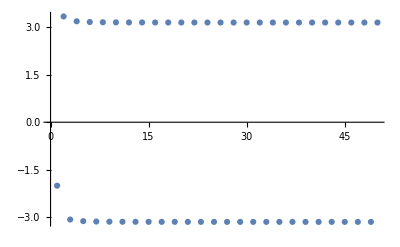

```mathematica
ListPlot[Table[N[a[n]],{n,1,50}]]
```

```mathematica
FullSimplify[a[n]]
```

((-1)^(1+n) (-2 (-1)^n+π-2 n π+2 (-1)^n (-1+2 n) LerchPhi[-1,1,1/2+n]))/(-1+2 n)

```mathematica
Sum[1/a[n],{n,1,Infinity}]
```

```mathematica
sequence={-2 I,(10 I)/3,-((46 I)/15),(334 I)/105,-((982 I)/315),(10942 I)/3465,-((140986 I)/45045),(28382 I)/9009};
ratios=Most[sequence]/Rest[sequence];
ratios
```

{-3/5,-25/23,-161/167,-501/491,-5401/5471,-71123/70493,-70493/70955}

```mathematica
5!
```

120

```mathematica
f[t]
```

f[t]

```mathematica
Integrate[(FourierTn[1,t]-FourierTn[0,t]/(2*Pi))*BesselJ[0,t],{t,-Infinity,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-4.81037×10^7}. NIntegrate obtained -0.999997-1.35612×10^-10 ⅈ and 0.0000438801 for the integral and error estimates.

-0.999997-1.35612×10^-10 ⅈ

```mathematica
NIntegrate[(FourierTn[1,t]-FourierTn[0,t]/(2*Pi)),{t,-Infinity,Infinity}]
```

-1.+4.18887×10^-13 ⅈ

```mathematica
FullSimplify[(FourierTn[1,t]-FourierTn[0,t]/(2*Pi))/-1]
```

```mathematica
Integrate[FourierTn[2,t]-(-2 ⅈ π t Cos[t]+(2 ⅈ π+t) Sin[t])/(π t^2),{t,-Infinity,Infinity}]
```

-1-2 π

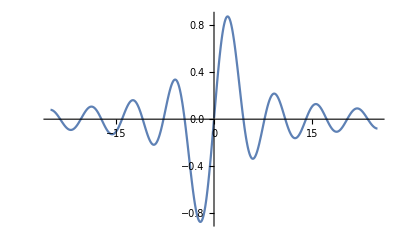

```mathematica
Plot[Im[Out[431]],{t,-25,25}]
```

```mathematica
Out[431]
```

(-2 ⅈ π t Cos[t]+(2 ⅈ π+t) Sin[t])/(π t^2)

```mathematica
Out[182]=Out[183]
```

Set::write: Tag Out in %182 is Protected.

(8 t Cos[t]+2 (-4+t^2) Sin[t])/t^3

```mathematica
Alpha[m,n]
```

0

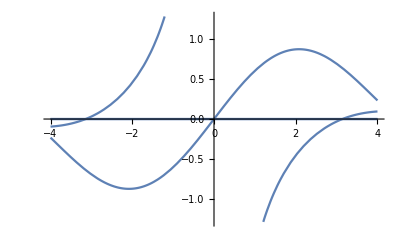

```mathematica
Plot[ReIm[{FourierTn[1,t],(2 ⅈ (-t Cos[t]+Sin[t]))/t^2}],{t,-4,4}]
```

```mathematica
(*Define symbolic inner product*)InnerProductSymbolic[f_,g_]:=NIntegrate[f*g*BesselJ[0,t],{t,-Infinity,Infinity},WorkingPrecision->20]

(*Define v1 and v2*)
v1=FourierTn[0,t];
v2=FourierTn[1,t];

(*Compute u1 by normalizing v1*)
norm1=Sqrt[InnerProductSymbolic[v1,v1]];
u1=FullSimplify[v1/norm1];

(*Compute the components for u2*)
innerProd1=InnerProductSymbolic[u1,v2];
innerProd2=InnerProductSymbolic[u1,u1];(*This should be 1 since u1 is normalized*)(*Compute u2 and normalize it*)u2Unnormalized=FullSimplify[v2-innerProd1/innerProd2*u1];
norm2=Sqrt[InnerProductSymbolic[u2Unnormalized,u2Unnormalized]];
u2=FullSimplify[u2Unnormalized/norm2];
```

NIntegrate::precw: The precision of the argument function (((ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t) BesselJ[0,t] («1»))/t) is less than WorkingPrecision (20.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0 and 3.1853604009017516801×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function ((BesselJ[0,t] (0. Cos[t]+«57» Sin[t])^2)/t^2) is less than WorkingPrecision (20.).

```mathematica
InnerProductWithU1=InnerProduct[u1,FourierTn[2,t]];
InnerProductWithU2=InnerProduct[u2,FourierTn[2,t]];

u3Unnormalized=FourierTn[2,t]-InnerProductWithU1*u1-InnerProductWithU2*u2;
u3Norm=Sqrt[InnerProduct[u3Unnormalized,u3Unnormalized]];

u3=u3Unnormalized/u3Norm;
```

Integrate::optx: Unknown option WorkingPrecision in Integrate[((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t) BesselJ[0,t] Conjugate[(ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t],{t,-∞,∞},WorkingPrecision→25].

$Aborted

Integrate::optx: Unknown option WorkingPrecision in Integrate[((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t) BesselJ[0,t] Conjugate[(ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t],{t,-∞,∞},WorkingPrecision→25].

Integrate::optx: Unknown option WorkingPrecision in Integrate[(((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t) BesselJ[0,t] Conjugate[ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t])/(√Integrate[(ⅈ Power[«2»] Power[«2»]-ⅈ Power[«2»] Power[«2»]) BesselJ[0,t] Conjugate[Times[«3»]+Times[«3»]],«1»,«16»→25]),{t,-∞,∞},WorkingPrecision→25].

General::stop: Further output of Integrate::optx will be suppressed during this calculation.

$Aborted

```mathematica
EInnerProduct[f_,g_]:=Integrate[f*Conjugate[g]*BesselJ[0,t],{t,-Infinity,Infinity}];
```

```mathematica
InnerProduct[f_,g_]:=Integrate[f*Conjugate[g]*BesselJ[0,t],{t,-Infinity,Infinity}];

u1=FourierTn[0,t]/Sqrt[InnerProduct[FourierTn[0,t],FourierTn[0,t]]];
u2=(FourierTn[1,t]-InnerProduct[u1,FourierTn[1,t]]*u1)/Sqrt[InnerProduct[FourierTn[1,t]-InnerProduct[u1,FourierTn[1,t]]*u1,FourierTn[1,t]-InnerProduct[u1,FourierTn[1,t]]*u1]];
```

$Aborted

Integrate::optx: Unknown option WorkingPrecision in Integrate[((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t) BesselJ[0,t] Conjugate[(ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t],{t,-∞,∞},WorkingPrecision→25].

$Aborted

```mathematica
u2
```

1.25658803879748240974167 ((1.16109122742189016160454×10^-54+1.54818288303966431771355×10^-39 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t)

```mathematica
u3Unnormalized=FourierTn[2,t]-InnerProduct[u1,FourierTn[2,t]]*u1-InnerProduct[u2,FourierTn[2,t]]*u2;
u3=u3Unnormalized/Sqrt[InnerProduct[u3Unnormalized,u3Unnormalized]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {169.6666666666666666666667}. NIntegrate obtained -1.258513886557358037936387-1.082845995188997161463038×10^-55 ⅈ and 0.00004647167864871656315327441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {255.}. NIntegrate obtained 8.234953041881355800084101×10^-55+1.371464652394229702832499×10^-39 ⅈ and 0.00006667722272556570152728138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {169.6666666666666666666667}. NIntegrate obtained -0.637116067695483289718368+1.615937527591678573816721×10^-54 ⅈ and 0.0002036986517603810593083922 for the integral and error estimates.

```mathematica
u3
```

(1.58879086601846254900566×10^-54-1.2528258941504849248253 ⅈ) (4 (-(ⅈ ⅇ^(-ⅈ t))/t^3+(ⅈ ⅇ^(ⅈ t))/t^3)-4 (-ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2)+(0.429992876686475416073977+3.69972925569721385036517×10^-56 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)-(1.03479434924870549095566×10^-54+1.72336607783213604067049×10^-39 ⅈ) ((1.16109122742189016160454×10^-54+1.54818288303966431771355×10^-39 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t)+(ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)

```mathematica
Integrate[u3*BesselJ[0,t],{t,-Infinity,Infinity}]
```

∫_(-∞)^∞ (1.58879086601846254900566×10^-54-1.2528258941504849248253 ⅈ) (4 (-(ⅈ ⅇ^(-ⅈ t))/t^3+(ⅈ ⅇ^(ⅈ t))/t^3)-4 (-ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2)+(0.429992876686475416073977+3.69972925569721385036517×10^-56 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)-(1.03479434924870549095566×10^-54+1.72336607783213604067049×10^-39 ⅈ) ((1.16109122742189016160454×10^-54+1.54818288303966431771355×10^-39 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t)+(ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t) BesselJ[0,t]ⅆt

```mathematica
u1
```

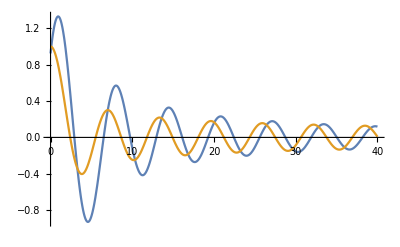

```mathematica
Plot[{Re[u1]-Im[u2]-Im[u3],BesselJ[0,t]},{t,0,40},PlotRange->All]
```

```mathematica
u3
```

```mathematica
{u1,u2,u3}
```

{0.3416671689358256895455703 ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t),1.25658803879748240974167 ((1.16109122742189016160454×10^-54+1.54818288303966431771355×10^-39 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t),(1.58879086601846254900566×10^-54-1.2528258941504849248253 ⅈ) (4 (-(ⅈ ⅇ^(-ⅈ t))/t^3+(ⅈ ⅇ^(ⅈ t))/t^3)-4 (-ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2)+(0.429992876686475416073977+3.69972925569721385036517×10^-56 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)-(1.03479434924870549095566×10^-54+1.72336607783213604067049×10^-39 ⅈ) ((1.16109122742189016160454×10^-54+1.54818288303966431771355×10^-39 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t)+(ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)}

```mathematica
u1=FourierTn[0,t]/Sqrt[EInnerProduct[FourierTn[0,t],FourierTn[0,t]]];
```

$Aborted

```mathematica
Integrate[FourierTn[5,t],{t,0,Infinity}]
```

-(46 ⅈ)/15

```mathematica
Integrate[FourierTn[6,t],{t,0,Infinity}]
```

-π

```mathematica
Integrate[FourierTn[7,t],{t,0,Infinity}]
```

(334 ⅈ)/105

```mathematica
Integrate[FourierTn[8,t],{t,0,Infinity}]
```

π

```mathematica
Integrate[FourierTn[9,t],{t,0,Infinity}]
```

-(982 ⅈ)/315

```mathematica
Integrate[FourierTn[11,t],{t,0,Infinity}]
```

(10942 ⅈ)/3465